```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BTCUSD_BTCUSD_25SEP20/";
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_Tiingo_LTC/";*)
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=Module[{v},
v=Catch[CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x], _SystemException];
If[NumberQ[v],v,0]
]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
(*Print["[calibrate] α, β: " <> ToString[{α,β}]];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];
target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
(*data[[1;;10]]*)
```

( | Date | PX_LAST | contract_name | BTC Price | log return future | log return bitcoin
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 40143.7 | 0.0212907 | 0.018658
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 39401.7 | -0.0904653 | -0.0934764
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 43262.4 | -0.0196938 | -0.0216123
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 44207.6 | -0.131645 | -0.126287
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 50158.3 | 0.03685 | 0.0328265
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 48538.5 | -0.119603 | -0.11567
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 54490.5 | -0.042369 | -0.0388241
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 56647.7 | 0.018947 | 0.0163419
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 55729.5 | -0.0359909 | -0.0331504)

```mathematica
data[[1;;10]]
```

( | datetime | spot | futures | rs | rf
0 | 2020-06-17 01:00:00 | 9479.56 | 9568.25 | -0.00502031 | -0.00484805
1 | 2020-06-17 02:00:00 | 9455.49 | 9542.25 | -0.00254238 | -0.00272102
2 | 2020-06-17 03:00:00 | 9439.89 | 9530.25 | -0.0016512 | -0.00125836
3 | 2020-06-17 04:00:00 | 9453.3 | 9549.5 | 0.00141956 | 0.00201785
4 | 2020-06-17 05:00:00 | 9459.25 | 9550.5 | 0.000629212 | 0.000104712
5 | 2020-06-17 06:00:00 | 9439.4 | 9523.75 | -0.00210068 | -0.00280483
6 | 2020-06-17 07:00:00 | 9472.49 | 9572.75 | 0.00349939 | 0.00513184
7 | 2020-06-17 08:00:00 | 9506.24 | 9613.5 | 0.00355662 | 0.00424784
8 | 2020-06-17 09:00:00 | 9490.43 | 9588.25 | -0.0016645 | -0.00262997)

```mathematica
data[[1,5]]
```

rs

```mathematica
data[[1,6]]
```

rf

```mathematica
α0=0.5; β0=0;
```

```mathematica
For[kk=9, kk≥0, kk--,
Print[kk];
SeedRandom[123456];
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,5⟧;
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,{6,5}⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

9

8

7

6

5

4

3

2

1

0

```mathematica
{α0,β0}
```

{0.918711,0.0675779}

```mathematica
dataDirectory
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../processed_data/BTCUSD_BTCUSD_25SEP20/

```mathematica
For[kk=0, kk≤185, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,5⟧;
(*dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;*)
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,6⟧;
rf=data2⟦2;;All,5⟧;
(*rs=data2⟦2;;All,7⟧;
rf=data2⟦2;;All,6⟧;*)
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

15

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

16

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

17

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

18

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

19

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

20

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

21

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

22

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

23

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

24

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

25

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

26

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

27

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

28

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

29

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

30

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

31

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

32

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

33

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

34

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

35

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

36

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

37

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

38

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

39

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

40

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

41

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

42

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

43

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

44

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

45

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

46

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

47

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

48

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

49

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

50

Risk Measures...

Variance

VaR 99

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

VaR 95

ES 99

ES 95

Spectral 10

51

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

52

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

53

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

54

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

55

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

56

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

57

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

58

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

59

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

60

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

61

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

62

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

63

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

64

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

65

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

66

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

67

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

68

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

69

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

70

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

71

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

72

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

73

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

74

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

75

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

76

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

77

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

78

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

79

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

80

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

81

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

82

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

83

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

84

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

85

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

86

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

87

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

88

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

89

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

90

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

91

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

92

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

93

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

94

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

95

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

96

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

97

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

98

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

99

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

100

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

101

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

102

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

103

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

104

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

105

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

106

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

107

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

108

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

109

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

110

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

111

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

112

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

113

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

114

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

115

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

116

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

117

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

118

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

119

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

120

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

121

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

122

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

123

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

124

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

125

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

126

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

127

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

128

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

129

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

130

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

131

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

132

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

133

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

134

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

135

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

136

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

137

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

138

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

139

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

140

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

141

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

142

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

143

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

144

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

145

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

146

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

147

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

148

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

149

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

150

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

151

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

152

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

153

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

154

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

155

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

156

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

157

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

158

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

159

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

160

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

161

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

162

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

163

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

164

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

165

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

166

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

167

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

168

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

169

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

170

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

171

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

172

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

173

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

174

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

175

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

176

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

177

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

178

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

179

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

180

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

181

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

182

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

183

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

184

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

185

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2020-06-17-01-00-00 | 0.82547 | 0.725483 | 0.645041 | 0.559725 | 0.605212 | 0.600373
 | 2020-06-17-05-00-00 | 0.822343 | 0.725368 | 0.648475 | 0.556385 | 0.604691 | 0.59739
 | 2020-06-17-09-00-00 | 0.818698 | 0.72337 | 0.649536 | 0.552131 | 0.602238 | 0.594078
 | 2020-06-17-13-00-00 | 0.820985 | 0.72471 | 0.649262 | 0.559332 | 0.606438 | 0.593396
 | 2020-06-17-17-00-00 | 0.821116 | 0.72797 | 0.660668 | 0.557304 | 0.606858 | 0.6003
 | 2020-06-17-21-00-00 | 0.813164 | 0.729525 | 0.654369 | 0.554231 | 0.593398 | 0.593358
 | 2020-06-18-01-00-00 | 0.808586 | 0.727874 | 0.644201 | 0.557378 | 0.591712 | 0.585521
 | 2020-06-18-05-00-00 | 0.801538 | 0.724498 | 0.644268 | 0.543545 | 0.583329 | 0.582193
 | 2020-06-18-09-00-00 | 0.803103 | 0.723103 | 0.637068 | 0.551975 | 0.584722 | 0.578311
 | 2020-06-18-13-00-00 | 0.829076 | 0.746316 | 0.675949 | 0.575433 | 0.617704 | 0.613356
 | 2020-06-18-17-00-00 | 0.830744 | 0.741343 | 0.675911 | 0.555771 | 0.635276 | 0.608678
 | 2020-06-18-21-00-00 | 0.832592 | 0.746327 | 0.684051 | 0.569883 | 0.642914 | 0.605305
 | 2020-06-19-01-00-00 | 0.825728 | 0.736392 | 0.668958 | 0.54741 | 0.627262 | 0.604136
 | 2020-06-19-05-00-00 | 0.830913 | 0.744809 | 0.660016 | 0.555965 | 0.63415 | 0.615112
 | 2020-06-19-09-00-00 | 0.82639 | 0.741766 | 0.649266 | 0.546428 | 0.627415 | 0.606515
 | 2020-06-19-13-00-00 | 0.823021 | 0.740309 | 0.654851 | 0.547658 | 0.628092 | 0.602073
 | 2020-06-19-17-00-00 | 0.816829 | 0.733653 | 0.644305 | 0.53918 | 0.619972 | 0.595369
 | 2020-06-19-21-00-00 | 0.808831 | 0.726152 | 0.637483 | 0.525132 | 0.610545 | 0.588127
 | 2020-06-20-01-00-00 | 0.815489 | 0.733172 | 0.647055 | 0.538204 | 0.620319 | 0.59641
 | 2020-06-20-05-00-00 | 0.810623 | 0.723457 | 0.657672 | 0.519706 | 0.612371 | 0.602104
 | 2020-06-20-09-00-00 | 0.816914 | 0.735043 | 0.650835 | 0.540227 | 0.623014 | 0.59742
 | 2020-06-20-13-00-00 | 0.813228 | 0.731694 | 0.643369 | 0.530879 | 0.616869 | 0.594471
 | 2020-06-20-17-00-00 | 0.815078 | 0.729884 | 0.648915 | 0.533417 | 0.619282 | 0.597851
 | 2020-06-20-21-00-00 | 0.819344 | 0.73405 | 0.650643 | 0.534716 | 0.620023 | 0.602664
 | 2020-06-21-01-00-00 | 0.811369 | 0.724984 | 0.656862 | 0.518665 | 0.612746 | 0.599333
 | 2020-06-21-05-00-00 | 0.812739 | 0.727895 | 0.651974 | 0.528057 | 0.615745 | 0.59548
 | 2020-06-21-09-00-00 | 0.821357 | 0.733291 | 0.682031 | 0.543803 | 0.631622 | 0.607002
 | 2020-06-21-13-00-00 | 0.804942 | 0.716977 | 0.666878 | 0.519632 | 0.609807 | 0.58377
 | 2020-06-21-17-00-00 | 0.802567 | 0.715848 | 0.661751 | 0.517635 | 0.606888 | 0.580015
 | 2020-06-21-21-00-00 | 0.797084 | 0.713689 | 0.657729 | 0.513297 | 0.602635 | 0.572505
 | 2020-06-22-01-00-00 | 0.794211 | 0.712547 | 0.641794 | 0.513885 | 0.595878 | 0.571216
 | 2020-06-22-05-00-00 | 0.79449 | 0.711433 | 0.658126 | 0.511982 | 0.601444 | 0.557344
 | 2020-06-22-09-00-00 | 0.796677 | 0.7097 | 0.65731 | 0.508927 | 0.598387 | 0.57195
 | 2020-06-22-13-00-00 | 0.797749 | 0.708985 | 0.645151 | 0.506491 | 0.593721 | 0.576019
 | 2020-06-22-17-00-00 | 0.798863 | 0.714039 | 0.640411 | 0.517199 | 0.594748 | 0.575301
 | 2020-06-22-21-00-00 | 0.800835 | 0.715557 | 0.648969 | 0.518964 | 0.602096 | 0.56327
 | 2020-06-23-01-00-00 | 0.798671 | 0.716794 | 0.648541 | 0.518738 | 0.601555 | 0.561117
 | 2020-06-23-05-00-00 | 0.800297 | 0.716779 | 0.652231 | 0.516913 | 0.602651 | 0.562312
 | 2020-06-23-09-00-00 | 0.798362 | 0.717874 | 0.645484 | 0.52447 | 0.60215 | 0.554798
 | 2020-06-23-13-00-00 | 0.795596 | 0.716652 | 0.628155 | 0.510504 | 0.596286 | 0.55565
 | 2020-06-23-17-00-00 | 0.797714 | 0.719422 | 0.637894 | 0.518016 | 0.602864 | 0.565111
 | 2020-06-23-21-00-00 | 0.798619 | 0.718755 | 0.633615 | 0.513125 | 0.600652 | 0.565493
 | 2020-06-24-01-00-00 | 0.795254 | 0.716335 | 0.628621 | 0.507338 | 0.596708 | 0.564043
 | 2020-06-24-05-00-00 | 0.797957 | 0.71851 | 0.630788 | 0.513777 | 0.600261 | 0.564641
 | 2020-06-24-09-00-00 | 0.796302 | 0.723932 | 0.619078 | 0.53463 | 0.580073 | 0.568633
 | 2020-06-24-13-00-00 | 0.79465 | 0.551901 | 0.611538 | 0.535404 | 0.553728 | 0.581886
 | 2020-06-24-17-00-00 | 0.807743 | 0.569291 | 0.644436 | 0.550179 | 0.576263 | 0.621939
 | 2020-06-24-21-00-00 | 0.792821 | 0.526213 | 0.594919 | 0.510696 | 0.541826 | 0.607676
 | 2020-06-25-01-00-00 | 0.793064 | 0.526427 | 0.596369 | 0.510778 | 0.54214 | 0.608401
 | 2020-06-25-05-00-00 | 0.801131 | 0.559952 | 0.602842 | 0.507726 | 0.536841 | 0.617579
 | 2020-06-25-09-00-00 | 0.79789 | 0.558016 | 0.602842 | 0.506249 | 0.535918 | 0.611829
 | 2020-06-25-13-00-00 | 0.814727 | 0.588076 | 0.581168 | 0.541063 | 0.564266 | 0.609261
 | 2020-06-25-17-00-00 | 0.813108 | 0.581661 | 0.642842 | 0.515984 | 0.576145 | 0.609657
 | 2020-06-25-21-00-00 | 0.813086 | 0.597225 | 0.674124 | 0.522245 | 0.591236 | 0.612097
 | 2020-06-26-01-00-00 | 0.808759 | 0.594714 | 0.660399 | 0.502986 | 0.586101 | 0.62392
 | 2020-06-26-05-00-00 | 0.804361 | 0.592007 | 0.651775 | 0.499044 | 0.582638 | 0.619464
 | 2020-06-26-09-00-00 | 0.794829 | 0.586873 | 0.625672 | 0.49382 | 0.563117 | 0.612365
 | 2020-06-26-13-00-00 | 0.796165 | 0.597854 | 0.592041 | 0.522438 | 0.570609 | 0.576137
 | 2020-06-26-17-00-00 | 0.787936 | 0.586847 | 0.545743 | 0.49901 | 0.531791 | 0.571981
 | 2020-06-26-21-00-00 | 0.787762 | 0.587006 | 0.544074 | 0.49877 | 0.53155 | 0.570574
 | 2020-06-27-01-00-00 | 0.789254 | 0.593172 | 0.563693 | 0.506614 | 0.538037 | 0.597057
 | 2020-06-27-05-00-00 | 0.782625 | 0.588523 | 0.586108 | 0.501923 | 0.538238 | 0.599219
 | 2020-06-27-09-00-00 | 0.781611 | 0.586358 | 0.582906 | 0.50281 | 0.537417 | 0.598735
 | 2020-06-27-13-00-00 | 0.779744 | 0.580614 | 0.591758 | 0.49852 | 0.539267 | 0.59439
 | 2020-06-27-17-00-00 | 0.782372 | 0.584353 | 0.596028 | 0.501205 | 0.542663 | 0.597043
 | 2020-06-27-21-00-00 | 0.788781 | 0.589024 | 0.586209 | 0.460028 | 0.516807 | 0.619015
 | 2020-06-28-01-00-00 | 0.799205 | 0.584543 | 0.581432 | 0.492563 | 0.514823 | 0.610538
 | 2020-06-28-05-00-00 | 0.799397 | 0.585929 | 0.574327 | 0.497085 | 0.514274 | 0.60743
 | 2020-06-28-09-00-00 | 0.806415 | 0.592855 | 0.595357 | 0.504316 | 0.526686 | 0.62408
 | 2020-06-28-13-00-00 | 0.803506 | 0.582184 | 0.592966 | 0.497572 | 0.522259 | 0.619033
 | 2020-06-28-17-00-00 | 0.807445 | 0.596486 | 0.588372 | 0.516087 | 0.545541 | 0.616956
 | 2020-06-28-21-00-00 | 0.802682 | 0.597306 | 0.598242 | 0.508757 | 0.5398 | 0.613295
 | 2020-06-29-01-00-00 | 0.807801 | 0.587362 | 0.616359 | 0.50195 | 0.542853 | 0.633993
 | 2020-06-29-05-00-00 | 0.812996 | 0.603521 | 0.598178 | 0.522635 | 0.548448 | 0.63733
 | 2020-06-29-09-00-00 | 0.813711 | 0.603551 | 0.599591 | 0.52482 | 0.550287 | 0.639597
 | 2020-06-29-13-00-00 | 0.81254 | 0.605186 | 0.603223 | 0.52315 | 0.551879 | 0.640297
 | 2020-06-29-17-00-00 | 0.808778 | 0.610593 | 0.617712 | 0.526263 | 0.547399 | 0.6275
 | 2020-06-29-21-00-00 | 0.812654 | 0.599903 | 0.619482 | 0.525257 | 0.559985 | 0.627652
 | 2020-06-30-01-00-00 | 0.804503 | 0.59119 | 0.644352 | 0.498762 | 0.554229 | 0.636007
 | 2020-06-30-05-00-00 | 0.810357 | 0.61057 | 0.617506 | 0.523219 | 0.557905 | 0.633043
 | 2020-06-30-09-00-00 | 0.809292 | 0.610593 | 0.622297 | 0.524212 | 0.559142 | 0.623763
 | 2020-06-30-13-00-00 | 0.815831 | 0.610593 | 0.633107 | 0.524271 | 0.563934 | 0.642356
 | 2020-06-30-17-00-00 | 0.811147 | 0.610593 | 0.617591 | 0.527958 | 0.55865 | 0.628885
 | 2020-06-30-21-00-00 | 0.808553 | 0.610593 | 0.595265 | 0.523973 | 0.555927 | 0.636448
 | 2020-07-01-01-00-00 | 0.809403 | 0.599824 | 0.616549 | 0.521247 | 0.560538 | 0.62811
 | 2020-07-01-05-00-00 | 0.799637 | 0.585895 | 0.614506 | 0.495467 | 0.54671 | 0.63324
 | 2020-07-01-09-00-00 | 0.797635 | 0.597866 | 0.583766 | 0.506695 | 0.541604 | 0.625469
 | 2020-07-01-13-00-00 | 0.79874 | 0.592925 | 0.595769 | 0.506944 | 0.544015 | 0.615736
 | 2020-07-01-17-00-00 | 0.801736 | 0.610593 | 0.648498 | 0.50576 | 0.564814 | 0.626347
 | 2020-07-01-21-00-00 | 0.805008 | 0.610593 | 0.658339 | 0.508856 | 0.571483 | 0.630699
 | 2020-07-02-01-00-00 | 0.807897 | 0.598817 | 0.617503 | 0.518048 | 0.560859 | 0.622179
 | 2020-07-02-05-00-00 | 0.810308 | 0.608623 | 0.624148 | 0.519533 | 0.564206 | 0.624967
 | 2020-07-02-09-00-00 | 0.816014 | 0.610593 | 0.632979 | 0.522725 | 0.577815 | 0.640176
 | 2020-07-02-13-00-00 | 0.816274 | 0.610593 | 0.627517 | 0.527324 | 0.582729 | 0.635369
 | 2020-07-02-17-00-00 | 0.816942 | 0.508116 | 0.676851 | 0.440653 | 0.559894 | 0.668191
 | 2020-07-02-21-00-00 | 0.809535 | 0.483857 | 0.646903 | 0.433585 | 0.544354 | 0.651754
 | 2020-07-03-01-00-00 | 0.811745 | 0.505258 | 0.67913 | 0.434232 | 0.559691 | 0.652184
 | 2020-07-03-05-00-00 | 0.809641 | 0.503677 | 0.677574 | 0.43133 | 0.556899 | 0.658357
 | 2020-07-03-09-00-00 | 0.811637 | 0.503625 | 0.678147 | 0.434195 | 0.559116 | 0.652151
 | 2020-07-03-13-00-00 | 0.813885 | 0.50738 | 0.684704 | 0.437261 | 0.563277 | 0.655117
 | 2020-07-03-17-00-00 | 0.825302 | 0.518068 | 0.675656 | 0.4666 | 0.574119 | 0.665702
 | 2020-07-03-21-00-00 | 0.822338 | 0.512475 | 0.655913 | 0.461859 | 0.565488 | 0.662059
 | 2020-07-04-01-00-00 | 0.821348 | 0.522607 | 0.694197 | 0.44755 | 0.572833 | 0.672022
 | 2020-07-04-05-00-00 | 0.819363 | 0.518309 | 0.693155 | 0.444372 | 0.570304 | 0.671796
 | 2020-07-04-09-00-00 | 0.8202 | 0.537536 | 0.712256 | 0.436953 | 0.573719 | 0.669189
 | 2020-07-04-13-00-00 | 0.819079 | 0.515348 | 0.691623 | 0.444136 | 0.569233 | 0.670732
 | 2020-07-04-17-00-00 | 0.817731 | 0.512056 | 0.689643 | 0.443913 | 0.567778 | 0.669761
 | 2020-07-04-21-00-00 | 0.810704 | 0.517036 | 0.645095 | 0.469769 | 0.565967 | 0.616903
 | 2020-07-05-01-00-00 | 0.810054 | 0.514462 | 0.642647 | 0.469476 | 0.564923 | 0.615077
 | 2020-07-05-05-00-00 | 0.811723 | 0.510595 | 0.650036 | 0.466764 | 0.563282 | 0.622545
 | 2020-07-05-09-00-00 | 0.810868 | 0.51311 | 0.63565 | 0.46929 | 0.556833 | 0.622152
 | 2020-07-05-13-00-00 | 0.82365 | 0.536697 | 0.656651 | 0.490731 | 0.56813 | 0.638895
 | 2020-07-05-17-00-00 | 0.825639 | 0.543764 | 0.646269 | 0.493953 | 0.572477 | 0.642898
 | 2020-07-05-21-00-00 | 0.830512 | 0.550364 | 0.655377 | 0.49814 | 0.578879 | 0.650709
 | 2020-07-06-01-00-00 | 0.832199 | 0.560749 | 0.657122 | 0.502085 | 0.582838 | 0.647159
 | 2020-07-06-05-00-00 | 0.827308 | 0.558339 | 0.64794 | 0.495279 | 0.577731 | 0.643936
 | 2020-07-06-09-00-00 | 0.8146 | 0.560646 | 0.641282 | 0.493367 | 0.579734 | 0.588342
 | 2020-07-06-13-00-00 | 0.808468 | 0.559225 | 0.646657 | 0.488869 | 0.575931 | 0.581202
 | 2020-07-06-17-00-00 | 0.816965 | 0.58585 | 0.684083 | 0.502098 | 0.596638 | 0.608825
 | 2020-07-06-21-00-00 | 0.809542 | 0.581228 | 0.667925 | 0.497591 | 0.591119 | 0.603009
 | 2020-07-07-01-00-00 | 0.801865 | 0.583039 | 0.640148 | 0.492732 | 0.582108 | 0.601954
 | 2020-07-07-05-00-00 | 0.798039 | 0.574807 | 0.634527 | 0.485653 | 0.576864 | 0.600166
 | 2020-07-07-09-00-00 | 0.803409 | 0.552033 | 0.634964 | 0.455616 | 0.559172 | 0.610279
 | 2020-07-07-13-00-00 | 0.80882 | 0.568574 | 0.666483 | 0.476016 | 0.570097 | 0.618974
 | 2020-07-07-17-00-00 | 0.809789 | 0.550201 | 0.644675 | 0.467133 | 0.563765 | 0.623213
 | 2020-07-07-21-00-00 | 0.810395 | 0.554582 | 0.651553 | 0.468709 | 0.568542 | 0.624841
 | 2020-07-08-01-00-00 | 0.808715 | 0.549801 | 0.643763 | 0.464439 | 0.562386 | 0.624647
 | 2020-07-08-05-00-00 | 0.802004 | 0.552215 | 0.631148 | 0.456993 | 0.557307 | 0.60354
 | 2020-07-08-09-00-00 | 0.799478 | 0.546485 | 0.626143 | 0.454771 | 0.552988 | 0.600887
 | 2020-07-08-13-00-00 | 0.799805 | 0.553493 | 0.630958 | 0.456708 | 0.554126 | 0.603466
 | 2020-07-08-17-00-00 | 0.800835 | 0.567729 | 0.627249 | 0.495758 | 0.573015 | 0.583314
 | 2020-07-08-21-00-00 | 0.799701 | 0.567311 | 0.636369 | 0.49529 | 0.574965 | 0.585368
 | 2020-07-09-01-00-00 | 0.797527 | 0.542582 | 0.658784 | 0.459711 | 0.559946 | 0.609651
 | 2020-07-09-05-00-00 | 0.797615 | 0.546544 | 0.662283 | 0.460239 | 0.562241 | 0.610146
 | 2020-07-09-09-00-00 | 0.796872 | 0.54711 | 0.659666 | 0.45872 | 0.562095 | 0.609474
 | 2020-07-09-13-00-00 | 0.801066 | 0.552833 | 0.670321 | 0.46875 | 0.569145 | 0.610239
 | 2020-07-09-17-00-00 | 0.782244 | 0.560332 | 0.624822 | 0.353128 | 0.503143 | 0.606726
 | 2020-07-09-21-00-00 | 0.774988 | 0.541631 | 0.632568 | 0.342768 | 0.502098 | 0.600229
 | 2020-07-10-01-00-00 | 0.778728 | 0.544511 | 0.635561 | 0.349371 | 0.506673 | 0.604127
 | 2020-07-10-05-00-00 | 0.782983 | 0.547705 | 0.641165 | 0.349011 | 0.50975 | 0.61081
 | 2020-07-10-09-00-00 | 0.797369 | 0.579897 | 0.646008 | 0.397825 | 0.537041 | 0.614801
 | 2020-07-10-13-00-00 | 0.792991 | 0.571583 | 0.622136 | 0.387538 | 0.522578 | 0.610236
 | 2020-07-10-17-00-00 | 0.787825 | 0.577642 | 0.628247 | 0.388951 | 0.529224 | 0.600979
 | 2020-07-10-21-00-00 | 0.794071 | 0.583344 | 0.634303 | 0.395662 | 0.531472 | 0.606429
 | 2020-07-11-01-00-00 | 0.795466 | 0.565306 | 0.654545 | 0.381159 | 0.544701 | 0.5976
 | 2020-07-11-05-00-00 | 0.792234 | 0.57975 | 0.631967 | 0.386489 | 0.546365 | 0.590711
 | 2020-07-11-09-00-00 | 0.789203 | 0.576901 | 0.628404 | 0.383886 | 0.542884 | 0.585963
 | 2020-07-11-13-00-00 | 0.797659 | 0.581973 | 0.646737 | 0.40098 | 0.537547 | 0.602501
 | 2020-07-11-17-00-00 | 0.802764 | 0.583499 | 0.65628 | 0.402829 | 0.541303 | 0.608114
 | 2020-07-11-21-00-00 | 0.788244 | 0.566096 | 0.647622 | 0.371398 | 0.517846 | 0.625402
 | 2020-07-12-01-00-00 | 0.792931 | 0.573263 | 0.649524 | 0.378152 | 0.521342 | 0.629416
 | 2020-07-12-05-00-00 | 0.825735 | 0.592168 | 0.695344 | 0.394057 | 0.549598 | 0.676077
 | 2020-07-12-09-00-00 | 0.799688 | 0.577225 | 0.652169 | 0.384285 | 0.526847 | 0.637275
 | 2020-07-12-13-00-00 | 0.810352 | 0.569655 | 0.620896 | 0.370467 | 0.510487 | 0.669903
 | 2020-07-12-17-00-00 | 0.81663 | 0.571552 | 0.601891 | 0.432838 | 0.521124 | 0.667958
 | 2020-07-12-21-00-00 | 0.803881 | 0.528076 | 0.578219 | 0.419933 | 0.523768 | 0.646239
 | 2020-07-13-01-00-00 | 0.782563 | 0.513241 | 0.570408 | 0.429575 | 0.513285 | 0.621513
 | 2020-07-13-05-00-00 | 0.80828 | 0.509996 | 0.565063 | 0.383499 | 0.4927 | 0.670845
 | 2020-07-13-09-00-00 | 0.825009 | 0.528077 | 0.599793 | 0.399026 | 0.517327 | 0.688119
 | 2020-07-13-13-00-00 | 0.815519 | 0.503924 | 0.576237 | 0.387844 | 0.499852 | 0.674868
 | 2020-07-13-17-00-00 | 0.822267 | 0.56985 | 0.618778 | 0.434267 | 0.529998 | 0.676335
 | 2020-07-13-21-00-00 | 0.802328 | 0.531537 | 0.596862 | 0.362982 | 0.468981 | 0.708152
 | 2020-07-14-01-00-00 | 0.816073 | 0.590456 | 0.60853 | 0.432648 | 0.501201 | 0.709077
 | 2020-07-14-05-00-00 | 0.811913 | 0.553557 | 0.56846 | 0.41154 | 0.47755 | 0.712221
 | 2020-07-14-09-00-00 | 0.816115 | 0.570176 | 0.619814 | 0.439787 | 0.505133 | 0.716651
 | 2020-07-14-13-00-00 | 0.819449 | 0.659707 | 0.64182 | 0.42261 | 0.529908 | 0.723697
 | 2020-07-14-17-00-00 | 0.8145 | 0.60693 | 0.593427 | 0.425123 | 0.505776 | 0.69663
 | 2020-07-14-21-00-00 | 0.811718 | 0.631503 | 0.643473 | 0.422794 | 0.533271 | 0.69568
 | 2020-07-15-01-00-00 | 0.817259 | 0.629568 | 0.617538 | 0.444959 | 0.533566 | 0.689926
 | 2020-07-15-05-00-00 | 0.824683 | 0.644467 | 0.652571 | 0.439494 | 0.547679 | 0.705638
 | 2020-07-15-09-00-00 | 0.834606 | 0.64057 | 0.624745 | 0.464531 | 0.548145 | 0.7025
 | 2020-07-15-13-00-00 | 0.836386 | 0.647972 | 0.653289 | 0.448273 | 0.561347 | 0.713365
 | 2020-07-15-17-00-00 | 0.824076 | 0.619637 | 0.63409 | 0.428368 | 0.539368 | 0.698676
 | 2020-07-15-21-00-00 | 0.818676 | 0.596827 | 0.589724 | 0.434932 | 0.523504 | 0.693762
 | 2020-07-16-01-00-00 | 0.832894 | 0.628075 | 0.656739 | 0.43719 | 0.574699 | 0.714842
 | 2020-07-16-05-00-00 | 0.828915 | 0.613933 | 0.667458 | 0.435501 | 0.565973 | 0.709803
 | 2020-07-16-09-00-00 | 0.824863 | 0.590036 | 0.615557 | 0.451213 | 0.550741 | 0.689527
 | 2020-07-16-13-00-00 | 0.832609 | 0.602189 | 0.621772 | 0.461136 | 0.559738 | 0.679791
 | 2020-07-16-17-00-00 | 0.835775 | 0.606158 | 0.620945 | 0.458974 | 0.561757 | 0.704436
 | 2020-07-16-21-00-00 | 0.844147 | 0.624647 | 0.633995 | 0.476406 | 0.575252 | 0.713536
 | 2020-07-17-01-00-00 | 0.833956 | 0.576051 | 0.579052 | 0.463644 | 0.544261 | 0.694113
 | 2020-07-17-05-00-00 | 0.845445 | 0.576655 | 0.608652 | 0.452782 | 0.549419 | 0.712295
 | 2020-07-17-09-00-00 | 0.82961 | 0.558819 | 0.538326 | 0.472525 | 0.529191 | 0.671683
 | 2020-07-17-13-00-00 | 0.83337 | 0.548911 | 0.555389 | 0.456045 | 0.524309 | 0.683188
 | 2020-07-17-17-00-00 | 0.835443 | 0.570994 | 0.55338 | 0.472544 | 0.537946 | 0.680089
 | 2020-07-17-21-00-00 | 0.844904 | 0.56818 | 0.590611 | 0.463705 | 0.544443 | 0.702077

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2020-06-17-01-00-00 | 0.872201 | 0.523087 | 0.606467 | 0.572873 | 0.601465 | 0.715186
 | 2020-06-17-05-00-00 | 0.799167 | 0.496784 | 0.578064 | 0.539278 | 0.571926 | 0.550148
 | 2020-06-17-09-00-00 | 0.994401 | 0.725966 | 0.690495 | 0.738058 | 0.69726 | 1.03564
 | 2020-06-17-13-00-00 | 0.831141 | 2.26353 | 4.6076 | 3.64365 | 4.45652 | 0.758713
 | 2020-06-17-17-00-00 | 0.842301 | 0.708103 | 0.750644 | 0.667384 | 0.741771 | 0.425778
 | 2020-06-17-21-00-00 | 0.529559 | 0.227571 | 0.261111 | 0.224221 | 0.254882 | -6.31468
 | 2020-06-18-01-00-00 | 0.70414 | 0.266872 | 0.313319 | 0.28135 | 0.309459 | 0.532144
 | 2020-06-18-05-00-00 | -0.886561 | 0.262157 | 0.310121 | 0.265636 | 0.304258 | -395.247
 | 2020-06-18-09-00-00 | 0.470374 | 0.405491 | 0.492885 | 0.427906 | 0.472647 | -0.262511
 | 2020-06-18-13-00-00 | 0.971699 | 0.781878 | 0.889306 | 0.779109 | 0.863512 | 0.755967
 | 2020-06-18-17-00-00 | 0.611591 | 0.088793 | 0.104211 | 0.0952142 | 0.100206 | 0.55676
 | 2020-06-18-21-00-00 | 0.920476 | 0.713362 | 0.818607 | 0.711605 | 0.788113 | 0.635519
 | 2020-06-19-01-00-00 | 0.932697 | 0.781075 | 0.918569 | 0.840203 | 0.88096 | 0.615464
 | 2020-06-19-05-00-00 | 0.532319 | -0.141915 | -0.292408 | -0.205774 | -0.24646 | 0.548564
 | 2020-06-19-09-00-00 | 0.836723 | 0.616599 | 0.621054 | 0.619115 | 0.61997 | 0.540094
 | 2020-06-19-13-00-00 | 0.187077 | 0.218883 | 0.252705 | 0.23262 | 0.242772 | -0.184008
 | 2020-06-19-17-00-00 | 0.4214 | 0.332211 | 0.389567 | 0.360548 | 0.375922 | -0.331378
 | 2020-06-19-21-00-00 | 0.831348 | 0.808892 | 0.749714 | 0.77486 | 0.757537 | 0.248306
 | 2020-06-20-01-00-00 | 0.612649 | -1.22618 | -1.39311 | -1.2037 | -1.30914 | 0.583565
 | 2020-06-20-05-00-00 | 0.648417 | 0.551128 | 0.521814 | 0.543744 | 0.53074 | 0.372041
 | 2020-06-20-09-00-00 | 0.783125 | 0.413529 | 0.488075 | 0.449144 | 0.470215 | 0.497448
 | 2020-06-20-13-00-00 | 0.793257 | 0.337781 | 0.403966 | 0.369047 | 0.388508 | 0.557065
 | 2020-06-20-17-00-00 | 0.939106 | 0.638359 | 0.715724 | 0.685921 | 0.69954 | 0.74638
 | 2020-06-20-21-00-00 | 0.921772 | 0.849638 | 0.54353 | 0.735804 | 0.613152 | 0.698811
 | 2020-06-21-01-00-00 | 0.674521 | 0.346235 | 0.238443 | 0.352415 | 0.281837 | 0.63841
 | 2020-06-21-05-00-00 | 0.892646 | 0.638144 | 0.77318 | 0.683867 | 0.736781 | 0.371532
 | 2020-06-21-09-00-00 | -1.89911 | -0.278106 | -0.334288 | -0.272234 | -0.320767 | -4.75899
 | 2020-06-21-13-00-00 | -1.17838 | 0.167087 | -0.247628 | 0.0831364 | -0.170467 | -0.980199
 | 2020-06-21-17-00-00 | 0.399092 | 0.176214 | 0.116932 | 0.162924 | 0.126831 | 0.034432
 | 2020-06-21-21-00-00 | 0.896543 | 0.464748 | -0.0667467 | 0.334914 | 0.0402899 | 0.76336
 | 2020-06-22-01-00-00 | 0.932922 | 0.567476 | 0.630562 | 0.555031 | 0.623524 | 0.839376
 | 2020-06-22-05-00-00 | 0.968667 | 0.81363 | 0.672512 | 0.786485 | 0.699973 | 0.85113
 | 2020-06-22-09-00-00 | 0.891889 | 0.462657 | 0.567596 | 0.480094 | 0.556102 | 0.708531
 | 2020-06-22-13-00-00 | 0.930321 | 0.40805 | 0.362603 | 0.397103 | 0.371479 | 0.741768
 | 2020-06-22-17-00-00 | 0.831732 | 0.728637 | 0.745403 | 0.717622 | 0.739736 | 0.516469
 | 2020-06-22-21-00-00 | 0.936095 | 0.753274 | 0.778773 | 0.789559 | 0.798621 | 0.760584
 | 2020-06-23-01-00-00 | 0.83951 | 0.595799 | 0.672043 | 0.595909 | 0.65347 | 0.591102
 | 2020-06-23-05-00-00 | -1.78673 | 0.140375 | 0.132547 | 0.140496 | 0.134218 | 2.08395
 | 2020-06-23-09-00-00 | 0.952593 | 0.71456 | 0.798475 | 0.701556 | 0.770146 | 0.766122
 | 2020-06-23-13-00-00 | 0.947119 | 0.358103 | 0.378071 | 0.358444 | 0.375063 | 0.973746
 | 2020-06-23-17-00-00 | 0.902081 | 0.620836 | 0.659463 | 0.61926 | 0.655003 | 0.677161
 | 2020-06-23-21-00-00 | -9.3336 | 7.93617 | 8.93901 | 7.92273 | 8.78306 | -0.0974008
 | 2020-06-24-01-00-00 | 0.989308 | 1.35499 | 1.04327 | 1.28175 | 1.10421 | 0.836626
 | 2020-06-24-05-00-00 | 0.983844 | 0.836684 | 0.925125 | 0.844954 | 0.90352 | 0.853905
 | 2020-06-24-09-00-00 | 0.68371 | -0.0924878 | -0.100196 | -0.0948326 | -0.0961389 | 0.519443
 | 2020-06-24-13-00-00 | 0.937691 | 0.462613 | 0.556894 | 0.500491 | 0.532195 | 0.766305
 | 2020-06-24-17-00-00 | 0.899336 | 0.411041 | 0.492985 | 0.38009 | 0.45124 | 0.817812
 | 2020-06-24-21-00-00 | 0.679229 | 0.295468 | 0.368607 | 0.294535 | 0.351655 | 0.578417
 | 2020-06-25-01-00-00 | 0.962005 | 0.800315 | 0.824331 | 0.799922 | 0.820172 | 0.676255
 | 2020-06-25-05-00-00 | 0.926217 | 0.223036 | 0.263031 | 0.215664 | 0.249291 | 0.785686
 | 2020-06-25-09-00-00 | 0.926416 | 0.690088 | 0.718661 | 0.667153 | 0.709627 | 0.762348
 | 2020-06-25-13-00-00 | 0.976504 | 0.709395 | 0.82919 | 0.686996 | 0.783342 | 1.03431
 | 2020-06-25-17-00-00 | 0.673145 | -0.401618 | -0.531598 | -0.352299 | -0.494409 | 0.787458
 | 2020-06-25-21-00-00 | 0.608737 | 0.187549 | -0.0469545 | 0.413553 | 0.133712 | 0.501963
 | 2020-06-26-01-00-00 | 0.192842 | 0.508496 | 0.493361 | 0.528393 | 0.500444 | -1.75203
 | 2020-06-26-05-00-00 | 0.886267 | 0.764822 | 0.752944 | 0.774754 | 0.760731 | -1.24677
 | 2020-06-26-09-00-00 | 0.975415 | 0.875055 | 0.879019 | 0.864937 | 0.877917 | 0.82127
 | 2020-06-26-13-00-00 | 0.939808 | 0.482149 | 0.573426 | 0.454817 | 0.544484 | 0.82177
 | 2020-06-26-17-00-00 | 0.830654 | 0.560135 | 0.561189 | 0.559322 | 0.560858 | 0.643291
 | 2020-06-26-21-00-00 | 0.990129 | 0.71829 | 0.717585 | 0.718854 | 0.717857 | 0.929938
 | 2020-06-27-01-00-00 | -1.3647 | -0.0930535 | -0.115204 | -0.0627177 | -0.106856 | -3.56509
 | 2020-06-27-05-00-00 | 0.851661 | 0.605665 | 0.610993 | 0.598488 | 0.609309 | 0.612951
 | 2020-06-27-09-00-00 | 0.944201 | 0.788309 | 0.868868 | 0.698513 | 0.839865 | 20.7343
 | 2020-06-27-13-00-00 | 0.432839 | 5.46568 | 6.08688 | 4.86211 | 5.90304 | 0.603578
 | 2020-06-27-17-00-00 | 0.950272 | 0.781668 | 0.751904 | 0.767494 | 0.762691 | 0.710906
 | 2020-06-27-21-00-00 | 0.372291 | -1.85127 | -2.15698 | -1.71395 | -2.07389 | 0.656639
 | 2020-06-28-01-00-00 | 0.736787 | -1.38464 | -1.62325 | -1.36259 | -1.52931 | 0.614229
 | 2020-06-28-05-00-00 | 0.74608 | 0.803064 | 0.804903 | 0.799131 | 0.810884 | 2.6644
 | 2020-06-28-09-00-00 | 0.736379 | 0.616442 | 0.710227 | 0.610285 | 0.684563 | 0.0473059
 | 2020-06-28-13-00-00 | 0.967403 | 0.758069 | 0.894219 | 0.74752 | 0.847887 | 0.822405
 | 2020-06-28-17-00-00 | 0.106746 | -0.0400626 | -0.0461613 | -0.0398005 | -0.0457939 | 0.122149
 | 2020-06-28-21-00-00 | 0.671445 | -16.8274 | -19.4213 | -16.7038 | -19.0965 | 0.630752
 | 2020-06-29-01-00-00 | 0.833818 | 0.839913 | 0.869627 | 0.831753 | 0.867152 | 0.343454
 | 2020-06-29-05-00-00 | 0.979891 | 0.742558 | 0.845904 | 0.733995 | 0.832662 | 0.975735
 | 2020-06-29-09-00-00 | 0.797666 | 0.428291 | 1.13318 | 0.37857 | 0.974327 | 0.576634
 | 2020-06-29-13-00-00 | 0.863037 | 0.550156 | 0.630664 | 0.543011 | 0.617086 | 0.680225
 | 2020-06-29-17-00-00 | 0.979812 | 0.818487 | 0.890165 | 0.812184 | 0.870147 | 0.828741
 | 2020-06-29-21-00-00 | 0.93999 | 0.373285 | 0.380803 | 0.362877 | 0.377332 | 0.857213
 | 2020-06-30-01-00-00 | 0.946973 | 0.661278 | 0.794324 | 0.657183 | 0.769382 | 0.818538
 | 2020-06-30-05-00-00 | 0.907382 | 0.701718 | 0.825189 | 0.696137 | 0.800668 | 0.245392
 | 2020-06-30-09-00-00 | 0.920056 | 0.52252 | 0.610257 | 0.518357 | 0.597644 | 0.87467
 | 2020-06-30-13-00-00 | 0.533824 | 0.21951 | 0.259827 | 0.217761 | 0.251583 | 0.362142
 | 2020-06-30-17-00-00 | 0.83348 | -2.1812 | -2.54753 | -2.1643 | -2.49167 | 0.85997
 | 2020-06-30-21-00-00 | 0.935438 | 0.718393 | 0.707901 | 0.718865 | 0.710044 | 0.843077
 | 2020-07-01-01-00-00 | 0.158943 | 0.482033 | 0.504509 | 0.433404 | 0.501103 | -1.09824
 | 2020-07-01-05-00-00 | -12.8819 | -0.908095 | -1.16669 | -0.890747 | -1.11753 | 2.14369
 | 2020-07-01-09-00-00 | 0.82156 | 0.635572 | 0.610802 | 0.636231 | 0.616633 | 0.534137
 | 2020-07-01-13-00-00 | 0.991405 | 0.897175 | 0.94214 | 0.891973 | 0.96217 | 0.792457
 | 2020-07-01-17-00-00 | 0.908249 | 0.735882 | 0.718999 | 0.725392 | 0.730994 | 1.59489
 | 2020-07-01-21-00-00 | 0.939796 | 0.499728 | 0.58575 | 0.494179 | 0.57669 | 0.83045
 | 2020-07-02-01-00-00 | 0.834654 | 0.356967 | 0.353129 | 0.362807 | 0.354473 | 0.808551
 | 2020-07-02-05-00-00 | 0.817598 | 0.539576 | 0.610773 | 0.535749 | 0.596247 | 0.128107
 | 2020-07-02-09-00-00 | 0.863405 | 0.801874 | 0.717661 | 0.805528 | 0.734847 | 0.0883358
 | 2020-07-02-13-00-00 | 0.896736 | -0.305714 | -0.357253 | -0.303278 | -0.349575 | 0.766241
 | 2020-07-02-17-00-00 | -0.272804 | -0.0528588 | -0.062001 | -0.0497578 | -0.0600716 | -0.423462
 | 2020-07-02-21-00-00 | 0.875475 | 0.702621 | 0.589667 | 0.721995 | 0.622936 | 0.654678
 | 2020-07-03-01-00-00 | 0.677111 | 0.512281 | 0.557981 | 0.447705 | 0.548334 | -0.0884009
 | 2020-07-03-05-00-00 | 0.985734 | 1.08497 | 1.19371 | 0.954859 | 1.16923 | 0.725278
 | 2020-07-03-09-00-00 | 0.972372 | 0.0625057 | 0.0677939 | 0.0543661 | 0.066572 | 0.997301
 | 2020-07-03-13-00-00 | 0.838173 | 0.0379597 | 0.0411276 | 0.0328971 | 0.040502 | 0.759839
 | 2020-07-03-17-00-00 | 0.858801 | -0.292087 | -0.315521 | -0.262895 | -0.313846 | 0.879402
 | 2020-07-03-21-00-00 | -0.475155 | 0.449569 | 0.30846 | 0.423036 | 0.370578 | -1.57583
 | 2020-07-04-01-00-00 | -0.0716581 | 0.34601 | 0.375372 | 0.302414 | 0.370662 | 49.1887
 | 2020-07-04-05-00-00 | 0.833712 | 0.702086 | 0.765323 | 0.613879 | 0.753339 | 0.437172
 | 2020-07-04-09-00-00 | 0.323386 | -1.20973 | -1.7162 | -0.806341 | -1.47599 | 0.388366
 | 2020-07-04-13-00-00 | 0.716976 | 0.252046 | 0.270988 | 0.217778 | 0.267193 | 0.789128
 | 2020-07-04-17-00-00 | 0.933382 | 0.76154 | 0.83636 | 0.665433 | 0.814572 | 0.705909
 | 2020-07-04-21-00-00 | 0.69273 | 0.214864 | -0.0821608 | 0.256277 | 0.0919578 | 0.577303
 | 2020-07-05-01-00-00 | 0.876527 | 0.636052 | 0.689448 | 0.590537 | 0.659806 | 0.495111
 | 2020-07-05-05-00-00 | 0.99014 | 0.907684 | 0.987189 | 0.808419 | 0.956219 | 0.873416
 | 2020-07-05-09-00-00 | 0.930575 | 0.743146 | 0.74156 | 0.752885 | 0.744875 | -1.11301
 | 2020-07-05-13-00-00 | 0.974582 | 0.949015 | 1.02532 | 0.918403 | 1.01066 | 0.638891
 | 2020-07-05-17-00-00 | 0.95002 | -2.73473 | -3.36834 | -2.35777 | -3.2444 | 0.909031
 | 2020-07-05-21-00-00 | 0.839319 | 0.898139 | 1.00148 | 0.836965 | 0.981565 | 0.621628
 | 2020-07-06-01-00-00 | 0.927149 | 0.742845 | 0.699598 | 0.770857 | 0.706078 | 0.865388
 | 2020-07-06-05-00-00 | -11.2651 | -1.3664 | -1.62577 | -1.20648 | -1.6146 | -3.82755
 | 2020-07-06-09-00-00 | 0.836656 | 0.70292 | 0.660278 | 0.582406 | 0.658669 | 0.457915
 | 2020-07-06-13-00-00 | 0.906205 | 0.553076 | 0.570941 | 0.652602 | 0.591617 | 0.809003
 | 2020-07-06-17-00-00 | 0.858661 | 0.661561 | 0.707579 | 0.633154 | 0.690978 | 0.565105
 | 2020-07-06-21-00-00 | 0.534817 | -0.45796 | -0.814478 | -0.143362 | -0.714586 | 0.540914
 | 2020-07-07-01-00-00 | 0.819227 | -0.00824173 | 0.216134 | 0.46886 | 0.228462 | 0.671962
 | 2020-07-07-05-00-00 | 0.94017 | 9.25194 | 8.5853 | 7.63158 | 8.53225 | 0.751505
 | 2020-07-07-09-00-00 | 0.987677 | 0.134421 | 0.395749 | 0.88995 | 0.409615 | 0.967687
 | 2020-07-07-13-00-00 | 0.955431 | 0.889532 | 0.753526 | 0.978445 | 0.798866 | 0.680327
 | 2020-07-07-17-00-00 | 0.897088 | 0.499424 | 0.531518 | 0.626379 | 0.533205 | 0.952693
 | 2020-07-07-21-00-00 | 0.757185 | 2.74584 | 2.59785 | 2.18876 | 2.58751 | 0.65695
 | 2020-07-08-01-00-00 | 0.945612 | 0.909891 | 0.901663 | 0.844358 | 0.901287 | 0.176123
 | 2020-07-08-05-00-00 | 0.917947 | 0.76797 | 0.843499 | 0.666471 | 0.834436 | 1.71952
 | 2020-07-08-09-00-00 | -1.79593 | 1.82753 | 1.87528 | 1.24083 | 1.73145 | 0.343776
 | 2020-07-08-13-00-00 | 0.548636 | 0.543157 | 0.561711 | 0.516435 | 0.564543 | 0.017489
 | 2020-07-08-17-00-00 | 0.940082 | 0.448559 | 0.415338 | 0.372589 | 0.415133 | 0.837237
 | 2020-07-08-21-00-00 | 0.957833 | 3.47409 | 3.11423 | 2.5718 | 3.09767 | 0.781361
 | 2020-07-09-01-00-00 | 0.970761 | 0.792654 | 0.824105 | 0.74576 | 0.822752 | 0.849207
 | 2020-07-09-05-00-00 | 0.876171 | 1.00986 | 0.979293 | 0.93074 | 0.980296 | 0.434573
 | 2020-07-09-09-00-00 | 0.684801 | 0.224535 | 0.0835137 | 0.368753 | 0.0885567 | 0.676811
 | 2020-07-09-13-00-00 | 0.40929 | 0.0127345 | 0.0490409 | 0.224601 | 0.0566106 | 0.488297
 | 2020-07-09-17-00-00 | 0.16765 | -0.00483075 | -0.120367 | 0.545315 | 0.00698741 | 0.189567
 | 2020-07-09-21-00-00 | 0.911028 | 0.537875 | 0.493001 | 0.604498 | 0.537489 | 0.770654
 | 2020-07-10-01-00-00 | 0.812154 | 0.712618 | 0.746311 | 0.672285 | 0.717108 | 3.47718
 | 2020-07-10-05-00-00 | 0.995524 | 0.89138 | 0.953553 | 0.814768 | 0.901302 | 0.943614
 | 2020-07-10-09-00-00 | 0.918377 | 0.800448 | 0.912305 | 0.698685 | 0.825614 | 0.64032
 | 2020-07-10-13-00-00 | 0.693902 | 0.239756 | 0.00786634 | 0.533362 | 0.237231 | 0.511088
 | 2020-07-10-17-00-00 | 0.87488 | 0.55727 | 0.551489 | 0.566504 | 0.557645 | 0.643349
 | 2020-07-10-21-00-00 | 0.94515 | 0.788544 | 0.785215 | 0.746709 | 0.787838 | 0.778197
 | 2020-07-11-01-00-00 | 0.432677 | 1.28342 | 5.69632 | -1.00287 | 3.27262 | 0.413542
 | 2020-07-11-05-00-00 | 0.559756 | 0.444368 | 0.438799 | 0.452923 | 0.444244 | 0.202883
 | 2020-07-11-09-00-00 | 0.784302 | 0.608892 | 0.700073 | 0.538297 | 0.638222 | 0.477892
 | 2020-07-11-13-00-00 | 0.940847 | 0.777145 | 0.794341 | 0.665992 | 0.791731 | 0.776718
 | 2020-07-11-17-00-00 | 0.924669 | 0.693858 | 0.776589 | 0.58979 | 0.705807 | 0.752575
 | 2020-07-11-21-00-00 | 0.868508 | 0.476248 | 0.566857 | 0.429846 | 0.537458 | 0.81572
 | 2020-07-12-01-00-00 | 0.918248 | 0.672451 | 0.792327 | 0.567817 | 0.734995 | 0.551822
 | 2020-07-12-05-00-00 | 0.815663 | 0.429255 | 0.546151 | 0.408267 | 0.497617 | 0.597125
 | 2020-07-12-09-00-00 | 0.907948 | 1.36641 | 0.858178 | 1.67467 | 1.11405 | 0.778418
 | 2020-07-12-13-00-00 | 0.917415 | 0.736328 | 0.807261 | 0.603575 | 0.745683 | 0.465219
 | 2020-07-12-17-00-00 | 0.979946 | 0.760595 | 0.804381 | 0.640031 | 0.792659 | -0.0081019
 | 2020-07-12-21-00-00 | 0.134767 | 3.3913 | 3.14241 | 1.96108 | 2.67485 | 0.46504
 | 2020-07-13-01-00-00 | 0.763936 | 8.57951 | 10.1693 | 4.11806 | 8.01161 | 0.730105
 | 2020-07-13-05-00-00 | 0.877509 | 0.7384 | 0.751344 | 0.661256 | 0.733294 | 0.640011
 | 2020-07-13-09-00-00 | 0.842135 | -0.45817 | -0.512594 | -0.403887 | -0.44224 | 0.951754
 | 2020-07-13-13-00-00 | 0.927784 | 0.717179 | 0.772855 | 0.60751 | 0.700294 | 0.75068
 | 2020-07-13-17-00-00 | 0.982377 | 0.849579 | 0.92342 | 0.736882 | 0.845372 | 0.931856
 | 2020-07-13-21-00-00 | 0.957413 | 0.666856 | 0.77736 | 0.5154 | 0.690453 | 0.93907
 | 2020-07-14-01-00-00 | 0.306354 | 0.0174954 | 0.0198904 | 0.0143604 | 0.0177139 | -0.00236525
 | 2020-07-14-05-00-00 | 0.952508 | 0.770452 | 0.772643 | 0.883418 | 0.832983 | 0.287081
 | 2020-07-14-09-00-00 | 0.999555 | 0.986017 | 0.994996 | 0.813453 | 1.015 | 0.901898
 | 2020-07-14-13-00-00 | 0.825824 | 95.6422 | 88.5036 | 3.74631 | 70.5933 | 0.76135
 | 2020-07-14-17-00-00 | 0.967315 | 0.901163 | 0.903163 | 0.692868 | 0.901414 | 0.663113
 | 2020-07-14-21-00-00 | 0.953143 | 0.816758 | 0.790601 | 0.581396 | 0.77812 | 0.827922
 | 2020-07-15-01-00-00 | 0.966856 | 0.65101 | 0.699428 | 0.960755 | 0.793515 | 0.780761
 | 2020-07-15-05-00-00 | 0.966942 | 0.874937 | 0.830268 | 0.61799 | 0.813914 | 0.886127
 | 2020-07-15-09-00-00 | 0.981734 | 0.820621 | 0.832912 | 0.779498 | 0.839194 | 0.891876
 | 2020-07-15-13-00-00 | 0.482802 | 0.0259054 | 0.036052 | 0.087406 | 0.0406574 | 0.439491
 | 2020-07-15-17-00-00 | 0.39543 | 0.036158 | 0.0781994 | 0.0955909 | 0.114992 | 0.125665
 | 2020-07-15-21-00-00 | 0.808845 | 0.601893 | 0.598095 | 0.54311 | 0.594007 | 0.551338
 | 2020-07-16-01-00-00 | 0.959446 | 0.927173 | 0.947146 | 0.872843 | 0.948726 | -0.651501
 | 2020-07-16-05-00-00 | 0.954862 | 0.81207 | 0.807411 | 0.586064 | 0.801353 | 0.780891
 | 2020-07-16-09-00-00 | 0.954005 | 0.852983 | 0.850172 | 0.708922 | 0.84201 | 0.833475
 | 2020-07-16-13-00-00 | 0.981032 | 0.876114 | 0.805249 | 0.736412 | 0.943311 | 0.871601
 | 2020-07-16-17-00-00 | 0.912636 | 1.95377 | 1.81009 | 0.80501 | 1.73164 | 0.87768
 | 2020-07-16-21-00-00 | 0.421205 | 0.154289 | 0.115553 | 0.615544 | 0.16355 | 0.0640798
 | 2020-07-17-01-00-00 | 0.495244 | 0.574545 | 0.554611 | 0.424282 | 0.538681 | 4.71697
 | 2020-07-17-05-00-00 | 0.967118 | -0.488463 | -0.250834 | 0.989629 | -0.228538 | 0.955916
 | 2020-07-17-09-00-00 | 0.658503 | 0.438857 | 0.418442 | 0.363204 | 0.425625 | 0.497188
 | 2020-07-17-13-00-00 | 0.987889 | 0.88973 | 0.867137 | 0.784137 | 0.885238 | 0.914943
 | 2020-07-17-17-00-00 | 0.909644 | 0.819478 | 0.777791 | 0.639924 | 0.756511 | 0.513925
 | 2020-07-17-21-00-00 | 0.920155 | 0.799881 | 0.786932 | 0.732134 | 0.798964 | 0.529529

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

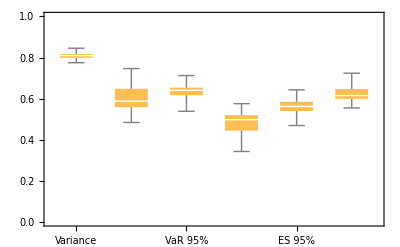

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
DateString[dates⟦1⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}]
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day", "Hour", "Minute", "Second"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

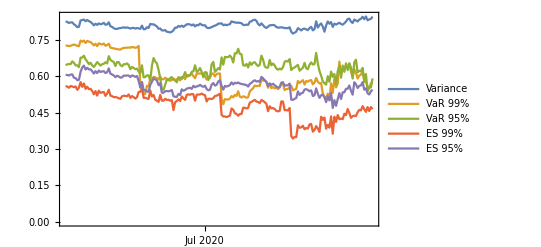

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

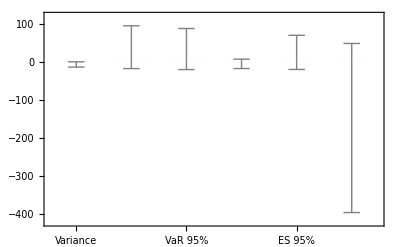

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day", "Hour", "Minute", "Second"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

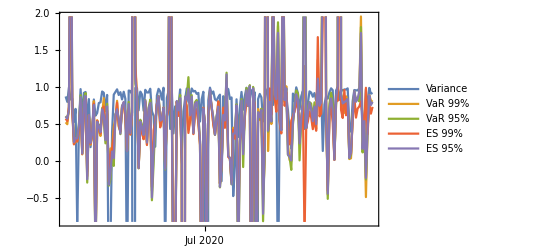

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,5]]
```

rs

```mathematica
data[[1,6]]
```

rf

```mathematica
data[[2,2]]
```

2020-07-17 21:00:00

### In-sample P&L

```mathematica
dates[[1]]
```

DateList[{2020-06-18,{Year,Month,Day,Hour,Minute,Second}}]

```mathematica
data[[2,2]]
```

2020-06-18 13:00:00

```mathematica
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];
```

```mathematica
For[kk=0, kk≤185, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,5⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day", "Hour", "Minute", "Second"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day", "Hour", "Minute", "Second"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | datetime | spot | futures | rs | rf
0 | 2020-07-17 21:00:00 | 9156.77 | 9241.75 | -0.000916934 | -0.000378644
1 | 2020-07-17 22:00:00 | 9151.75 | 9232.75 | -0.000548379 | -0.000974316
2 | 2020-07-17 23:00:00 | 9163.06 | 9237.25 | 0.00123507 | 0.000487277
3 | 2020-07-18 00:00:00 | 9155. | 9241.75 | -0.000880006 | 0.000487039
4 | 2020-07-18 01:00:00 | 9151.73 | 9233.75 | -0.000357246 | -0.000866012
5 | 2020-07-18 02:00:00 | 9143.84 | 9228.25 | -0.000862504 | -0.000595818
6 | 2020-07-18 03:00:00 | 9143.54 | 9227.75 | -0.0000328095 | -0.0000541829
7 | 2020-07-18 04:00:00 | 9138.4 | 9227.75 | -0.000562304 | 0.
8 | 2020-07-18 05:00:00 | 9144.61 | 9231.75 | 0.000679319 | 0.000433381)

```mathematica
hvec
```

{{2020-07-17-21-00-00},{0.917164},{0.900788},{0.929552},{0.708373},{0.902825},{0.987063},{{0.006497168110009817, {h$375187566 -> 0.9007881053526414}},{0.002511257029316975, {h$375187566 -> 0.9295524776919158}},{0.009758694684404066, {h$375187566 -> 0.7083725532123967}},{0.005092951465298618, {h$375187566 -> 0.9028254407012971}},{0.002765075745694761, {h$375187566 -> 0.9870633611826879}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤185, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,5⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

21.9.2022, BTC hourly: I stopped here as there is some issue with the date format, but the stuff below is not needed for the paper revision anyway.

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤185, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,5⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day", "-", "Hour", "-", "Minute", "-", "Second"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk<=185, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[ToExpression[#]&/@StringSplit[data⟦k,2⟧, {" ", "-", ":"}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,5⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day","-", "Hour", "-", "Minute", "-", "Second"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day","-", "Hour", "-", "Minute", "-", "Second"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤185, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

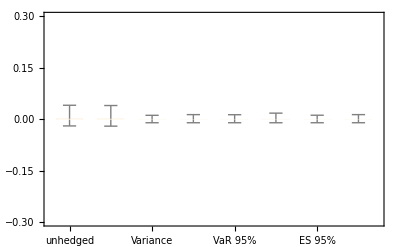

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

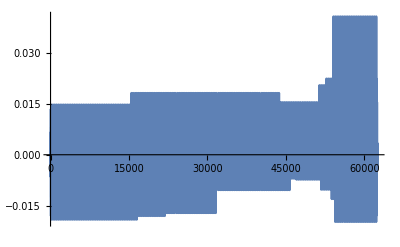

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤185, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

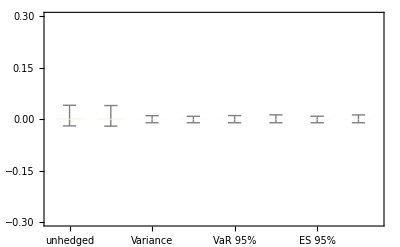

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
d[[3,1]]
```

2020-07-01

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day", "Hour", "Minute", "Second"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

DateString::str: String 2020-07-01 cannot be interpreted as a date in format {Year,Month,Day,Hour,Minute,Second}.

General::stop: Further output of DateString::str will be suppressed during this calculation.

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],0.000271636},{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],0.00152253},«7»,{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],-0.00159699},«734»} is not a valid dataset or list of datasets.

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],0.000151062},{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],0.00124877},«7»,{DateList[{2020-07-01,{Year,Month,Day,Hour,Minute,Second}}],-0.00167852},«734»} is not a valid dataset or list of datasets.

{DateListPlot[(1),PlotRange→{-0.25,0.25}],DateListPlot[(1),PlotRange→{-0.25,0.25}]}
 |  |  |  |

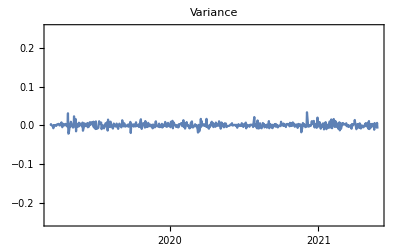
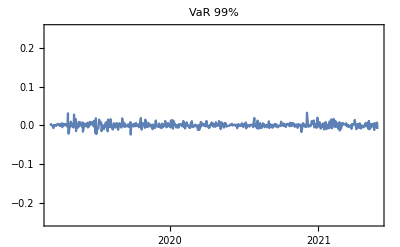
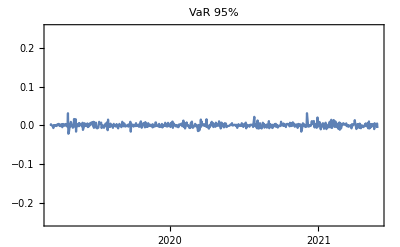
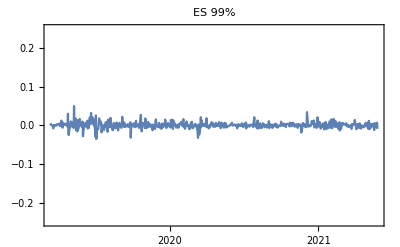
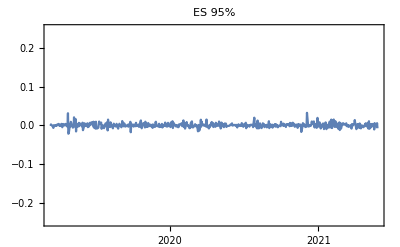
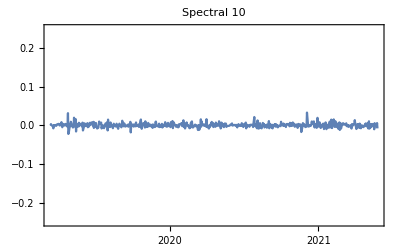

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

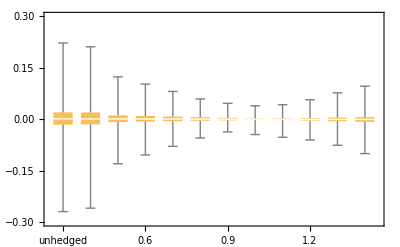

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

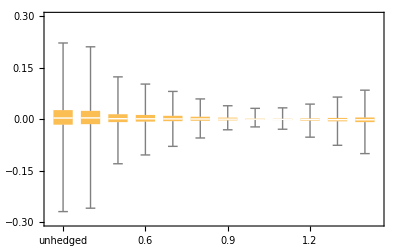

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤111, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 0.944958 | 0.936403 | 0.960422 | 0.939858 | 0.95253 | 0.949929
2021-05-13 | 0.944997 | 0.939292 | 0.95798 | 0.939858 | 0.950929 | 0.955053
2021-05-06 | 0.944795 | 0.939567 | 0.957988 | 0.939858 | 0.950902 | 0.955056
2021-04-29 | 0.945655 | 0.939858 | 0.957783 | 0.939858 | 0.951419 | 0.953189
2021-04-22 | 0.945022 | 0.939858 | 0.956836 | 0.939858 | 0.951895 | 0.95783
2021-04-15 | 0.943477 | 0.939858 | 0.957584 | 0.939858 | 0.950425 | 0.956884
2021-04-08 | 0.943478 | 0.939858 | 0.957346 | 0.939858 | 0.950425 | 0.957729
2021-04-01 | 0.944295 | 0.939858 | 0.957436 | 0.939858 | 0.950425 | 0.960253
2021-03-25 | 0.944517 | 0.939858 | 0.957748 | 0.939858 | 0.950425 | 0.957551
2021-03-18 | 0.944912 | 0.939858 | 0.958286 | 0.939858 | 0.950425 | 0.951931
2021-03-11 | 0.944109 | 0.939858 | 0.95762 | 0.939858 | 0.950425 | 0.949216
2021-03-04 | 0.9438 | 0.939858 | 0.957367 | 0.939858 | 0.950425 | 0.951002
2021-02-25 | 0.942553 | 0.939858 | 0.957789 | 0.939858 | 0.950686 | 0.951244
2021-02-18 | 0.943591 | 0.939858 | 0.957953 | 0.939858 | 0.950722 | 0.952645
2021-02-10 | 0.943575 | 0.939858 | 0.957789 | 0.939858 | 0.950686 | 0.951534
2021-02-03 | 0.942488 | 0.939858 | 0.957548 | 0.939858 | 0.950425 | 0.948618
2021-01-27 | 0.943994 | 0.939858 | 0.957388 | 0.939858 | 0.950425 | 0.951436
2021-01-20 | 0.943575 | 0.933217 | 0.957789 | 0.939858 | 0.950425 | 0.94659
2021-01-12 | 0.942291 | 0.939858 | 0.958821 | 0.939858 | 0.950425 | 0.951074
2021-01-05 | 0.937763 | 0.939858 | 0.926461 | 0.939858 | 0.941973 | 0.950224
2020-12-28 | 0.939688 | 0.942848 | 0.935498 | 0.931769 | 0.950043 | 0.948606
2020-12-18 | 0.938988 | 0.930508 | 0.940857 | 0.930508 | 0.948615 | 0.948099
2020-12-11 | 0.937418 | 0.930508 | 0.93659 | 0.929982 | 0.948912 | 0.948502
2020-12-04 | 0.937351 | 0.930508 | 0.937615 | 0.930508 | 0.948485 | 0.945604
2020-11-27 | 0.940641 | 0.949384 | 0.958542 | 0.937226 | 0.951376 | 0.946668
2020-11-19 | 0.941777 | 0.948722 | 0.958542 | 0.935753 | 0.951305 | 0.948856
2020-11-12 | 0.942044 | 0.96104 | 0.940723 | 0.953136 | 0.953458 | 0.943633
2020-11-05 | 0.940802 | 0.942962 | 0.934453 | 0.927417 | 0.950425 | 0.939673
2020-10-29 | 0.94099 | 0.96104 | 0.937759 | 0.952019 | 0.951658 | 0.943262
2020-10-22 | 0.940562 | 0.939867 | 0.93415 | 0.926782 | 0.950425 | 0.940401
2020-10-15 | 0.938923 | 0.938557 | 0.93375 | 0.926837 | 0.950425 | 0.940648
2020-10-08 | 0.939694 | 0.942708 | 0.933299 | 0.928603 | 0.950344 | 0.941757
2020-10-01 | 0.937485 | 0.924236 | 0.929361 | 0.922275 | 0.949601 | 0.939241
2020-09-24 | 0.937893 | 0.926261 | 0.924532 | 0.923896 | 0.950097 | 0.942868
2020-09-17 | 0.938604 | 0.943226 | 0.929538 | 0.923896 | 0.949641 | 0.944185
2020-09-10 | 0.938103 | 0.928079 | 0.929361 | 0.924417 | 0.949641 | 0.939386
2020-09-02 | 0.946997 | 0.96261 | 0.952165 | 0.959915 | 0.969274 | 0.938439
2020-08-26 | 0.951508 | 0.974346 | 0.95186 | 0.957458 | 0.968364 | 0.948049
2020-08-19 | 0.952679 | 0.968305 | 0.934266 | 0.966517 | 0.969688 | 0.948099
2020-08-12 | 0.952895 | 0.967749 | 0.934488 | 0.966633 | 0.969688 | 0.948492
2020-08-05 | 0.95096 | 0.941415 | 0.946592 | 0.95572 | 0.961297 | 0.945351
2020-07-29 | 0.952553 | 0.973319 | 0.952524 | 0.957899 | 0.968558 | 0.950066
2020-07-22 | 0.955108 | 0.973169 | 0.950411 | 0.958416 | 0.968558 | 0.954573
2020-07-15 | 0.953608 | 0.958604 | 0.956209 | 0.952615 | 0.967411 | 0.962158
2020-07-08 | 0.954 | 0.960096 | 0.957235 | 0.953315 | 0.967629 | 0.952328
2020-06-30 | 0.948643 | 0.938719 | 0.948944 | 0.935451 | 0.964035 | 0.946958
2020-06-23 | 0.948852 | 0.937191 | 0.948944 | 0.935109 | 0.964034 | 0.947431
2020-06-16 | 0.949394 | 0.93732 | 0.948944 | 0.935916 | 0.964202 | 0.947068
2020-06-09 | 0.950762 | 0.928101 | 0.944033 | 0.926849 | 0.963285 | 0.965948
2020-06-02 | 0.950521 | 0.931507 | 0.943374 | 0.927556 | 0.96335 | 0.965397
2020-05-26 | 0.950143 | 0.985633 | 0.946615 | 0.924463 | 0.961017 | 0.964796
2020-05-18 | 0.949726 | 0.973912 | 0.946639 | 0.923013 | 0.961372 | 0.964141
2020-05-11 | 0.949043 | 0.924443 | 0.942083 | 0.922073 | 0.961265 | 0.962554
2020-05-04 | 0.948231 | 0.939595 | 0.952671 | 0.957876 | 0.952671 | 0.953638
2020-04-27 | 0.948305 | 0.943333 | 0.948617 | 0.965464 | 0.953125 | 0.94799
2020-04-20 | 0.947418 | 0.932229 | 0.951637 | 0.967081 | 0.956018 | 0.948411
2020-04-13 | 0.946247 | 0.974895 | 0.94906 | 0.963845 | 0.950352 | 0.948831
2020-04-03 | 0.946647 | 0.972179 | 0.948412 | 0.962009 | 0.956572 | 0.953347
2020-03-27 | 0.946869 | 1.00313 | 0.957267 | 0.931201 | 0.965361 | 0.955997
2020-03-20 | 0.948047 | 0.932019 | 0.945609 | 0.927565 | 0.961887 | 0.954419
2020-03-13 | 0.940912 | 0.990325 | 0.951484 | 0.915055 | 0.954039 | 0.948019
2020-03-06 | 0.952808 | 0.981084 | 0.969034 | 0.894546 | 0.966617 | 0.981311
2020-02-28 | 0.951281 | 0.974535 | 0.928525 | 0.92524 | 0.949669 | 0.972828
2020-02-21 | 0.945766 | 0.96834 | 0.929343 | 0.912902 | 0.947423 | 0.944412
2020-02-13 | 0.947609 | 0.972418 | 0.96335 | 0.907758 | 0.954059 | 0.954091
2020-02-06 | 0.949967 | 0.968464 | 0.969217 | 0.910579 | 0.947851 | 0.970498
2020-01-30 | 0.945028 | 0.987854 | 0.964551 | 0.894115 | 0.956116 | 0.950736
2020-01-23 | 0.945315 | 0.991206 | 0.973714 | 0.889839 | 0.962378 | 0.951877
2020-01-15 | 0.943978 | 0.895572 | 0.975917 | 0.890487 | 0.97419 | 0.956251
2020-01-08 | 0.942792 | 0.888685 | 0.981181 | 0.884826 | 0.965118 | 0.936911
2019-12-31 | 0.942787 | 0.903469 | 0.979171 | 0.883563 | 0.964381 | 0.954428
2019-12-23 | 0.937528 | 0.905962 | 0.962848 | 0.858632 | 0.958957 | 0.942796
2019-12-16 | 0.940426 | 0.906818 | 0.965785 | 0.862065 | 0.960032 | 0.948748
2019-12-09 | 0.940839 | 0.896899 | 0.965173 | 0.862906 | 0.960506 | 0.947723
2019-12-02 | 0.940577 | 0.928648 | 0.964508 | 0.859172 | 0.955141 | 0.94551
2019-11-22 | 0.941498 | 0.908013 | 0.984811 | 0.862425 | 0.960168 | 0.95208
2019-11-15 | 0.939936 | 0.90337 | 0.978352 | 0.85984 | 0.958581 | 0.95817
2019-11-08 | 0.941661 | 0.907919 | 0.985419 | 0.86262 | 0.960159 | 0.952459
2019-11-01 | 0.941527 | 0.929728 | 0.967677 | 0.859583 | 0.955072 | 0.948766
2019-10-25 | 0.942203 | 0.900304 | 0.973538 | 0.865457 | 0.961747 | 0.950274
2019-10-18 | 0.942618 | 0.921892 | 0.977259 | 0.867404 | 0.962414 | 0.946753
2019-10-11 | 0.943893 | 0.922422 | 0.966945 | 0.863127 | 0.960883 | 0.952272
2019-10-04 | 0.944615 | 0.976721 | 0.989154 | 0.87093 | 0.971163 | 0.954409
2019-09-27 | 0.945315 | 0.907969 | 0.978127 | 0.867928 | 0.964172 | 0.954875
2019-09-20 | 0.94772 | 0.918224 | 0.971904 | 0.862493 | 0.961773 | 0.958886
2019-09-13 | 0.94814 | 0.91219 | 0.976634 | 0.867404 | 0.962962 | 0.955369
2019-09-06 | 0.949256 | 0.900032 | 0.966959 | 0.86491 | 0.961401 | 0.963012
2019-08-29 | 0.948447 | 0.905568 | 0.983225 | 0.86835 | 0.967502 | 0.960036
2019-08-22 | 0.949349 | 0.897549 | 0.9765 | 0.866493 | 0.962111 | 0.953764
2019-08-15 | 0.949441 | 0.902986 | 0.982439 | 0.867701 | 0.967015 | 0.959643
2019-08-08 | 0.950159 | 0.897288 | 0.988252 | 0.865484 | 0.963519 | 0.969646
2019-08-01 | 0.950575 | 0.898312 | 0.990852 | 0.869066 | 0.963959 | 0.967383
2019-07-25 | 0.952708 | 0.904081 | 0.977705 | 0.873133 | 0.963862 | 0.962677
2019-07-18 | 0.954122 | 0.912066 | 0.986841 | 0.872194 | 0.964292 | 0.963211
2019-07-11 | 0.954632 | 0.904948 | 0.981671 | 0.877109 | 0.962495 | 0.970682
2019-07-03 | 0.955577 | 0.909995 | 0.971198 | 0.877107 | 0.963871 | 0.963649
2019-06-26 | 0.952699 | 0.890509 | 0.977367 | 0.83414 | 0.959233 | 0.983879
2019-06-19 | 0.948754 | 0.94835 | 0.955752 | 0.823502 | 0.950703 | 0.959149
2019-06-12 | 0.949835 | 0.940703 | 0.976824 | 0.831524 | 0.963893 | 0.963056
2019-06-05 | 0.952382 | 0.936468 | 0.973488 | 0.829031 | 0.967053 | 0.959272
2019-05-29 | 0.953816 | 0.9319 | 0.973078 | 0.828212 | 0.966652 | 0.960235
2019-05-21 | 0.952927 | 0.910769 | 0.960888 | 0.817208 | 0.952976 | 0.961782
2019-05-14 | 0.954353 | 0.925084 | 0.97557 | 0.824959 | 0.960902 | 0.957063
2019-05-07 | 0.958395 | 0.938385 | 0.988898 | 0.842331 | 0.969916 | 0.974121
2019-04-30 | 0.959189 | 0.931491 | 0.989477 | 0.853378 | 0.973908 | 0.958102
2019-04-23 | 0.968071 | 0.960433 | 0.976322 | 0.889152 | 0.973911 | 0.987324
2019-04-15 | 0.968985 | 0.966333 | 0.990623 | 0.899854 | 0.973283 | 0.97487
2019-04-08 | 0.968988 | 0.953813 | 0.982515 | 0.885351 | 0.982884 | 0.978232
2019-04-01 | 0.967466 | 0.983798 | 0.997575 | 0.937425 | 0.992702 | 0.963878
2019-03-25 | 0.975057 | 0.964903 | 1.06264 | 0.954191 | 1.02416 | 0.971195
2019-03-18 | 0.974561 | 0.996531 | 0.998379 | 0.952044 | 1.0254 | 0.95721
2019-03-11 | 0.975732 | 0.957384 | 0.999247 | 0.960651 | 1.03466 | 0.971906)

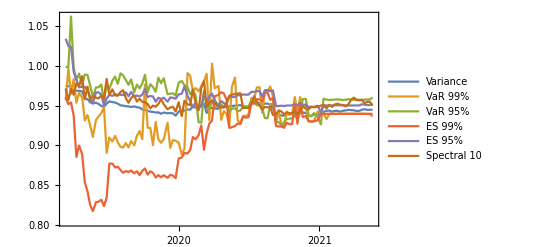

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```